Test Statistics

(N of Items | 5
Sample Size | 10
Mean | 2.6
SE of Mean | 0.476095
SD | 1.50555
Skewness | -0.0988433
Kurtosis | 2.24798
Min | 0
Max | 5)

Item Statistics

(Item | Number of Respondents | Correct Response Rate | Item Threshold | Item-Total Correlation
Item01 | 10 | 0.6 | -0.253347 | 0.565945
Item02 | 10 | 0.4 | 0.253347 | 0.59167
Item03 | 10 | 0.9 | -1.28155 | 0.546109
Item04 | 10 | 0.3 | 0.524401 | 0.715025
Item05 | 10 | 0.4 | 0.253347 | 0.463046)

Section 8.1.2 Adjacency Matrix

( | Item01 | Item02 | Item03 | Item04 | Item05
Item01 | 0 | 1 | 0 | 0 | 0
Item02 | 0 | 0 | 1 | 1 | 0
Item03 | 0 | 0 | 0 | 0 | 1
Item04 | 0 | 0 | 0 | 0 | 1
Item05 | 0 | 0 | 0 | 0 | 0)

Section 8.1.8 Directed Acyclic Graph

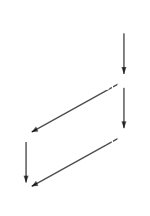

Your graph is a connected DAG.

Section 8.3 Parameter Learning

( | PIRP 1 | PIRP 2 | PIRP 3 | PIRP 4
Item01 | 0.6 |  |  | 
Item02 | 0.25 | 0.5 |  | 
Item03 | 0.833333 | 1. |  | 
Item04 | 0.166667 | 0.5 |  | 
Item05 | 0. | NaN(0/0) | 0.333333 | 0.666667)

Conditional Correct Response Rate

(Child Item | N of Parent Items | Parent Item(s) | Parent Item Response Pattern | Conditional Correct Response Rate
Item01 | 0 | No Parents | No Pattern | 0.6
Item02 | 1 | Item01  | 0 | 0.25
Item02 | 1 | Item01  | 1 | 0.5
Item03 | 1 | Item02  | 0 | 0.833333
Item03 | 1 | Item02  | 1 | 1.
Item04 | 1 | Item02  | 0 | 0.166667
Item04 | 1 | Item02  | 1 | 0.5
Item05 | 2 | Item03, Item04  | 00 | 0.
Item05 | 2 | Item03, Item04  | 01 | NaN(0/0)
Item05 | 2 | Item03, Item04  | 10 | 0.333333
Item05 | 2 | Item03, Item04  | 11 | 0.666667)

Section 8.4 Model Fit

(Model | Bayesian Network Model
Log-Likelihood(Benchmark Model) | -8.93517
Log-Likelihood(Null Model) | -28.8823
Chi-square(Null Model) | 39.8943
DF(Null Model) | 25
Log-Likelihood(Analysis Model) | -26.4114
Chi-square(Analysis Model) | 34.9525
DF(Analysis Model) | 20
NFI | 0.123872
RFI | 0
IFI | 0.248402
TLI | 0
CFI | 0
RMSEA | 0.288218
AIC | -5.04747
CAIC | -13.0054
BIC | -11.0992)

```mathematica
(*----------------------------------------------------*)
(*       Shojima, K. (30/04/2022)                          *)
(*          Bayesian network model on Mathematica.         *)
(*          http://shojima.starfree.jp/tde/                *)
(*----------------------------------------------------*)

(*DATA SPECIFICATION*)

(*Specify the file name of your data.*)
datafile="J5S10.csv";
(*Put the data file in the same folder where this Mathematica program is placed.*)
(*Do not delete the folder named as "mod."*)

(*Specify the row number in which the item labels are input. The program considers the reponse data start from the next row.*)
itemlabelrow=1;

(*Specify the column number in which the student IDs are input. The program considers the reponse data start from the next column.*)
studentIDcolumn=1;

(*The missing indicator must be a numerical value.*)
mi=-99;

(*----------------------------------------------------*)
(*ANALYSIS SETTING*)

(*Specify the structure of your model to be analyzed.*)
edgefile="EdgesBNM.csv";
(*Put the CSV file in the same folder where this Mathematica program is placed.*)

(*----------------------------------------------------*)
(*GRAPH OPTIONS: Note that the graph is not always well arranged.*)

(*Specify the label and graph sizes in the path diagram.*)
labelsize=15;
graphsize=150;
(*The diagram is not displayed if the version of your Mathematica is less than 12.*)

(*Position the cursor anywhere in the program commands and hit [shift+enter], and the program runs.*)
(*----------------------------------------------------*)
dir=NotebookDirectory[];
NotebookEvaluate[dir<>"mod\Module_BNM.nb"];
bnm[data];
(*----------------------------------------------------*)
```